r::shdw: Symbol r appears in multiple contexts {logisticRegression`,cephalon`}; definitions in context logisticRegression` may shadow or be shadowed by other definitions.

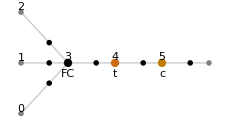
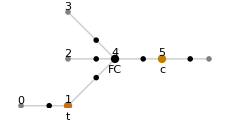
NetChain[<>] | -Graphics- | -Graphics- | <|{1,Biases}→{0.},{1,Weights}→{{-1.06865,1.412}}|> | -Graphics3D-
NetChain[<>] | -Graphics- | -Graphics- | <|{2,Biases}→{0.},{2,Weights}→{{-0.187075,1.22255}}|> | -Graphics3D-

```mathematica
Clear[r];
<<logisticRegression`
Grid[{{
net=NetInitialize@NetChain[
{1,Tanh},
"Input"->2,
"Output"->NetDecoder["Scalar"]],
NetInformation[net,"MXNetNodeGraphPlot"],
NetInformation[net,"SummaryGraphic"],
NetInformation[net,"Arrays"],
Plot3D[{net[{x,y}],-0.45x+0.09y+1},{x,0.1,1},{y,0.1,1},PlotLegends->"Expressions"]},
{net2=NetInitialize@NetChain[
{Tanh,1},
"Input"->2,
"Output"->NetDecoder["Scalar"]],
NetInformation[net2,"MXNetNodeGraphPlot"],
NetInformation[net2,"SummaryGraphic"],
NetInformation[net2,"Arrays"],
Plot3D[{net2[{x,y}],-0.45x+0.09y+1},{x,0.1,1},{y,0.1,1},PlotLegends->"Expressions"]}

},Frame->All]
```

## data

```mathematica
m=2.3;b=-5.85;
left=Cases[square,{x_,y_}/; EuclideanDistance[{x,y},{8,2}]<4];
right=Cases[square,{x_,y_}/; EuclideanDistance[{x,y},{0.5,10}]<5];data3=((#->0)&/@left)~Join~((#->1)&/@right);
```

## plot func

```mathematica
nett[{x_,y_}]:=x
```

```mathematica
plotSolution[net_,t_,{m_,b_}]:=Overlay[{
underneath=Rotate[ArrayPlot[Table[net[{x,y}],{x,0,10},{y,0,10}],Frame->False,ColorRules->{0->Gray,1->White}],π/2],
Show[Plot[m x+b,{x,0,10},PlotRange->{{0,10},{0,10}},PlotTheme->"Detailed",PlotStyle->{Red,Thickness[.02]},AspectRatio->1],
ListPlot[left,PlotStyle->Green,AspectRatio->1],
ListPlot[right,PlotStyle->Red,AspectRatio->1]]
}
];
```

```mathematica
Clear[r]
```

```mathematica
<<logisticRegression`
```

```mathematica
trained=NetTrain[net,data3,MaxTrainingRounds->Quantity[20,"Seconds"],Method->{"SGD","LearningRate"->0.1},TargetDevice->{"GPU",3},TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch,Abs[#WeightsVector⟦1;;2⟧]]&,"Interval"->0.01}];
plotSolution[trained,1]
```

plotSolution[NetChain[<>],1]

### The weights exist in a different space from the decision boundary and it does not really make sense to plot them here.

```mathematica
gradientNorms[assoc_]:=BarChart[Log[Max[Abs[#]]]&/@assoc,ChartLabels->Automatic,BarOrigin->Right];
```

```mathematica
trained=NetTrain[net,data3,MaxTrainingRounds->Quantity[10,"Seconds"],Method->{"SGD","LearningRate"->0.0001},TargetDevice->{"GPU",3},TrainingProgressReporting->{Function[#],"Interval"->Quantity[.5,"Seconds"]}]
```

NetChain[<>]

```mathematica
SS
```

```mathematica
1
```

1

```mathematica
NetInformation[net]
```